```mathematica
f[x_]:=x*Sin[x]*Cos[x];

GeneralTaylor[f_,x_,x0_,order_] := (
Block[{y,result,i},
result = f[x0];
For[i = 1, i<=order,++i,
result += (((x-x0)^n)/i!)*D[f[y],{y,i}]
];
N[result/.y->x0]
]
)
```

```mathematica
GraphicsRow[{Plot[{f[x],GeneralTaylor[x,2.5,10]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],GeneralTaylor[x,5,4]},{x,0,10},PlotRange->{{0,10},{-10,10}}],
Plot[{f[x],GeneralTaylor[x,7,4]},{x,0,10},PlotRange->{{0,10},{-10,10}}]}]
```

-Graphics-

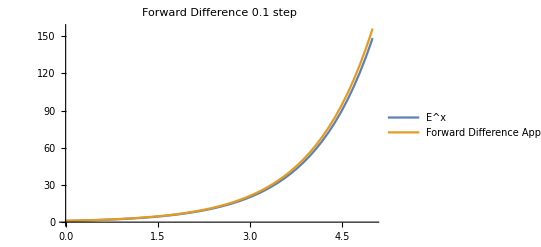

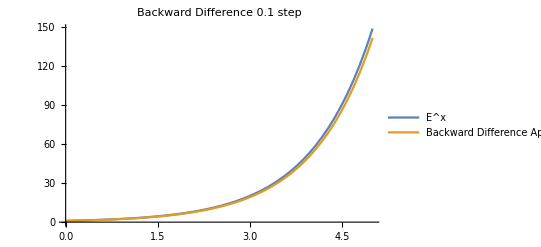

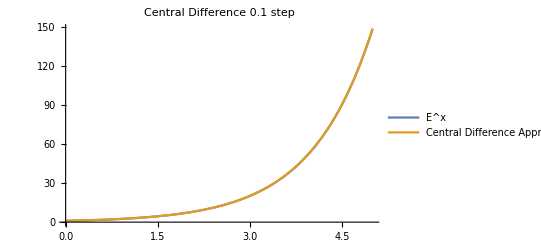

```mathematica
(*Razliki napred nazad i centralna*)

f[x_]:=E^x
forward[x_,dt_]:=(f[x+dt]-f[x])/dt
backward[x_,dt_]:=(f[x]-f[x-dt])/dt
central[x_,dt_]:=(f[x+dt]-f[x-dt])/(2dt)
Print[Plot[{f[x],forward[x,0.1]},{x,0,5},PlotLabel->"Forward Difference 0.1 step",PlotLegends->{"E^x","Forward Difference Approximation"}]];
Print[Plot[{f[x],backward[x,0.1]},{x,0,5},PlotLabel->"Backward Difference 0.1 step",PlotLegends->{"E^x","Backward Difference Approximation"}]];
Print[Plot[{f[x],central[x,0.1]},{x,0,5},PlotLabel->"Central Difference 0.1 step",PlotLegends->{"E^x","Central Difference Approximation"}]];
```